```mathematica
(*Module that solves for a field given an intial guess for the field value. The argument is a list: {initial guess of field (double), and shooter (boolean)}. If shooter is true, the method returns a pair of points {ϕ[end of integration] - ϕcosmological,ϕ0 (initial guess)} for ease of plotting. If shooter is false, the method returns the interpolation functions as a list {phi -> interior solution,ϕe -> exterior solution.*)
```

```mathematica
startI = 0.000001;
endI = 1.001;
startE = 1;
endE = 1000;
Λ = .10;
ρ = 10;
Rscaled = 1;
```

```mathematica
backgroundsolution[args_]:= Module[
{ϕcosmological = args[[1]]/10000,
Shooter = args[[2]],
ϕ0 = args[[1]]},

backgroundsolutioninterior= NDSolve[{1/Rscaled^2 D[ϕ[r],r,r]+2/(r Rscaled)D[ϕ[r],r]+2/Λ^2(4/(r Rscaled)D[ϕ[r],r]+ 2/(r^2 Rscaled^2)(D[ϕ[r],r])^2)==8π ρ,ϕ'[startI] ==0,ϕ[startI] ==  ϕ0},
ϕ,{r,startI,endI}];
backgroundsolutionexterior=NDSolve[{1/Rscaled^2 D[ϕe[r],r,r]+2/(r Rscaled)D[ϕe[r],r]+2/Λ^2(4/(r Rscaled)D[ϕe[r],r]+ 2/(r^2 Rscaled^2)(D[ϕe[r],r])^2)==0,ϕe[startE] ==  ϕ[1]/.backgroundsolutioninterior,ϕe'[startE] == ϕ'[1]/.backgroundsolutioninterior},
ϕe,{r,startE,endE}];
Proximity= (ϕe[endE]/.backgroundsolutionexterior) -ϕcosmological;
If[Shooter,Prepend[Proximity,ϕ0],{backgroundsolutioninterior,backgroundsolutionexterior}]
]
```

```mathematica
(*Solutions = Table[backgroundsolution[{x,True}],{x,Range[Trialstart,Trialend,Trialstep]}];*)
```

```mathematica
(*Solutions = Parallelize[Table[backgroundsolution[{x,True}],{x,Range[Trialstart,Trialend,Trialstep]}]];*)
```

```mathematica
(*Shooter method evaluation and plotting for range from Trialstart to Trialend for step size Trialstep. Plots point {Subscript[ϕ, 0],ϕ-ϕcosmological (as defined in backgroundsolution)}*)
```

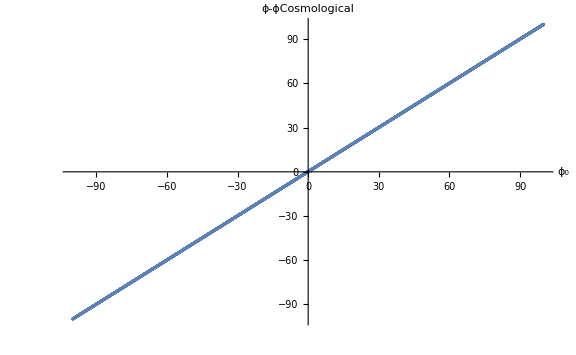

```mathematica
With[{Trialend = 100,
Trialstart = -100},Trialstep = (Trialend-Trialstart)/10000;
solutions = Parallelize[Table[backgroundsolution[{x,True}],{x,Range[Trialstart,Trialend,Trialstep]}]];
interpolatedFunction = Interpolation[solutions];
ListPlot[solutions,AxesLabel->{"ϕ_0","ϕ-ϕCosmological"},ImageSize->Large]]
```

```mathematica
(*Evaluation and plotting of a specific intial guess*)
```

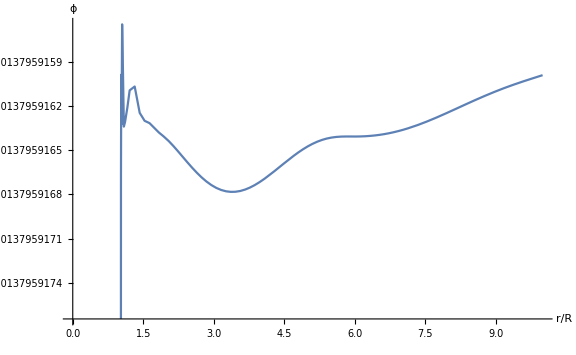

```mathematica
root = x/.FindRoot[interpolatedFunction[x],{x,0}];
sol=backgroundsolution[{root,False}];
Plot[Piecewise[{{ϕ[r]/.sol[[1]],r<1},{ϕe[r]/.sol[[2]],r>1}}],{r,0.000001,10},ImageSize->Large,AxesLabel->{"r/R","ϕ"}]
```

```mathematica
(*Perturbed Solution Based on Above Background Solution*)
```

```mathematica
perturbedsolution[args_]:= Module[
{ϕcosmological = args[[1]]/10000,
Shooter = args[[2]],
δ0 = args[[1]],
ω = π,
endtime = 100},
source[t_] := 3 Sin[ω Rscaled t];
perturbedsolutioninterior= NDSolve[{1/Rscaled^2 D[δ[r,t],r,r]+2/(r Rscaled)D[δ[r,t],r]-D[δ[r,t],t,t]+2/Λ^2(4/(r Rscaled)D[δ[r,t],r](ϕ''[r]/.sol[[1]])+4/(r Rscaled)D[δ[r,t],r,r](ϕ'[r]/.sol[[1]])+ 2/(r^2 Rscaled^2)(D[δ[r,t],r])-(ϕ''[r]/.sol[[1]] )D[δ[r,t],t,t]-D[δ[r,t],t,t](ϕ'[r]/.sol[[1]])4/r)==8π source[t],δ'[startI,t] ==0,δ[startI,t] ==  0,δ[r,0] == 0},
δ,{r,startI,endI},{t,0,endtime}];
perturbedsolutionexterior=NDSolve[{1/Rscaled^2 D[δe[r,t],r,r]+2/(r Rscaled)D[δe[r,t],r]-D[δe[r,t],t,t]+2/Λ^2(4/(r Rscaled)D[δe[r,t],r](ϕe''[r]/.sol[[2]])+4/(r Rscaled)D[δe[r,t],r,r](ϕe'[r]/.sol[[2]])+ 2/(r^2 Rscaled^2)(D[δe[r,t],r])-(ϕe''[r]/.sol[[2]] )D[δe[r,t],t,t]-D[δe[r,t],t,t](ϕe'[r]/.sol[[2]])4/r)==0,δe'[startE,t] ==(δ'[1,t] /.perturbedsolutioninterior),δe[startE,t] ==  (δ[1,t]/.perturbedsolutioninterior),δe[r,0] == 0},
δe,{r,startI,endI},{t,0,endtime}];
Proximity= (δe[endE]/.perturbedsolutionexterior) -0;
If[Shooter,Prepend[Proximity,δ0],{perturbedsolutioninterior,perturbedsolutionexterior}]
]
```

```mathematica
{1,True}[[1]]
```

1

```mathematica
perturbedsolution[{1,True}]
```

NDSolve::derlen: The length of the derivative operator Derivative[1] in δ'[1.×10^-6,t] is not the same as the number of arguments.

ReplaceAll::reps: {NDSolve[{{-(«1»)^(«2»)[«2»]+2 Power[«2»] («1»)^(«2»)[«2»]+δ^(2,0)[r,t]+200. Plus[«5»]}==24 π Sin[π t],δ'[1.×10^-6,t]==0,δ[1.×10^-6,t]==0,δ[r,0]==0},δ,{r,1.×10^-6,1.001},{t,0,100}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::derlen: The length of the derivative operator Derivative[1] in δe'[1,t] is not the same as the number of arguments.

ReplaceAll::reps: {NDSolve[{{-(«1»)^(«2»)[«2»]+2 Power[«2»] («1»)^(«2»)[«2»]+δe^(2,0)[r,t]+200. Plus[«5»]}==0,δe'[1,t]==(δ'[1,t]/.NDSolve[{Equal[«2»],Equal[«2»],Equal[«2»],Equal[«2»]},δ,{r,1.×10^-6,1.001},{t,0,100}]),δe[1,t]==(δ[1,t]/.NDSolve[{Equal[«2»],Equal[«2»],Equal[«2»],Equal[«2»]},δ,{r,1.×10^-6,1.001},{t,0,100}]),δe[r,0]==0},δe,{r,1.×10^-6,1.001},{t,0,100}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::argt: ReplaceAll called with 3 arguments; 1 or 2 arguments are expected.

ReplaceAll[1,δe[1000],NDSolve[{{-δe^(0,2)[r,t]+(2 δe^(1,0)[r,t])/r+δe^(2,0)[r,t]+200. (-(4 InterpolatingFunction[…][r] δe^(0,2)[r,t])/r-InterpolatingFunction[…][r] δe^(0,2)[r,t]+(2 δe^(1,0)[r,t])/r^2+(4 InterpolatingFunction[…][r] δe^(1,0)[r,t])/r+(4 InterpolatingFunction[…][r] δe^(2,0)[r,t])/r)}==0,δe'[1,t]==(δ'[1,t]/.NDSolve[{{-δ^(0,2)[r,t]+(2 δ^(1,0)[r,t])/r+δ^(2,0)[r,t]+200. (-(4 InterpolatingFunction[…][r] δ^(0,2)[r,t])/r-InterpolatingFunction[…][r] δ^(0,2)[r,t]+(2 δ^(1,0)[r,t])/r^2+(4 InterpolatingFunction[…][r] δ^(1,0)[r,t])/r+(4 InterpolatingFunction[…][r] δ^(2,0)[r,t])/r)}==24 π Sin[π t],δ'[1.×10^-6,t]==0,δ[1.×10^-6,t]==0,δ[r,0]==0},δ,{r,1.×10^-6,1.001},{t,0,100}]),δe[1,t]==(δ[1,t]/.NDSolve[{{-δ^(0,2)[r,t]+(2 δ^(1,0)[r,t])/r+δ^(2,0)[r,t]+200. (-(4 InterpolatingFunction[…][r] δ^(0,2)[r,t])/r-InterpolatingFunction[…][r] δ^(0,2)[r,t]+(2 δ^(1,0)[r,t])/r^2+(4 InterpolatingFunction[…][r] δ^(1,0)[r,t])/r+(4 InterpolatingFunction[…][r] δ^(2,0)[r,t])/r)}==24 π Sin[π t],δ'[1.×10^-6,t]==0,δ[1.×10^-6,t]==0,δ[r,0]==0},δ,{r,1.×10^-6,1.001},{t,0,100}]),δe[r,0]==0},δe,{r,1.×10^-6,1.001},{t,0,100}]]